```mathematica
Reals
```

ℝ

```mathematica
set=Reals
```

ℝ

```mathematica
Subsets@set
```

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[].

Subsets[ℝ]

```mathematica
{∅,Reals}
```

{∅,ℝ}

```mathematica
circle={Cos[t],Sin[t]}
```

{Cos[t],Sin[t]}

```mathematica
(D[circle,{t,2}].D[circle,t])/(√(circle.circle))
```

0

```mathematica
(D[circle,{t,2}].D[circle,t])/Norm[D[circle,t]]
```

0

```mathematica
k2[α_]:=□/□
```

```mathematica
circle'[t]
```

{Cos[t],Sin[t]}'[t]

```mathematica
J[{a_,b_}]:={-b,a}
```

```mathematica
(D[circle,{t,2}]. J[D[circle,t]])/Norm[D[circle,t]]^3
```

(Cos[t]^2+Sin[t]^2)/((Abs[Cos[t]]^2+Abs[Sin[t]]^2)^(3/2))

```mathematica
FullSimplify[(Cos[t]^2+Sin[t]^2)/((Abs[Cos[t]]^2+Abs[Sin[t]]^2)^(3/2)),t∈Reals]
```

1

```mathematica
Normalize@circle
```

{Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
With[{x=Cos,y=Sin},
(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3)
]
```

1/(√(Cos[t]^2+Sin[t]^2))

```mathematica
With[{x=Cos,y=Sin},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

1

```mathematica
With[{x=Cos,y=Sin},
FullSimplify[1/((x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3)),t∈Reals]
]
```

1

```mathematica
With[{x=Identity,y=Identity},
FullSimplify[1/((x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3)),t∈Reals]
]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
With[{x=Identity,y=Identity},
FullSimplify[1/((x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3)),t∈Reals]
]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
With[{x=Identity,y=Identity},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

0

```mathematica
With[{x=Identity,y=x^2},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

((x^2)''[t])/((1+((x^2)'[t])^2)^(3/2))

```mathematica
With[{x=Identity,y=t^2},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

((t^2)''[t])/((1+((t^2)'[t])^2)^(3/2))

```mathematica
With[{x=Identity,y=Sin},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

-Sin[t]/((1+Cos[t]^2)^(3/2))

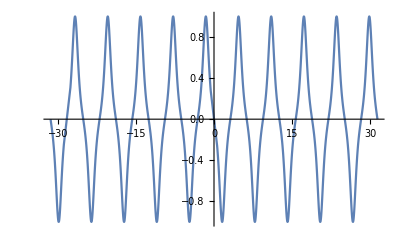

```mathematica
Plot[-Sin[t]/((1+Cos[t]^2)^(3/2)),{t,-10 π,10 π}]
```

```mathematica
With[{x=Identity,y=Function[x,x^2]},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

2/((1+4 t^2)^(3/2))

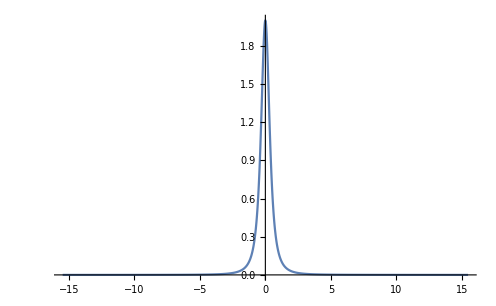

```mathematica
Plot[2/((1+4 t^2)^(3/2)),{t,-15.469999999999999,15.469999999999999},PlotRange->Full]
```

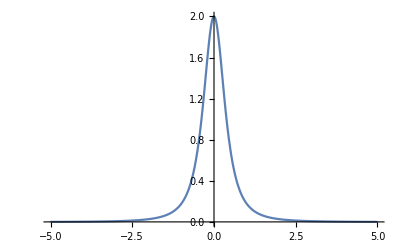

```mathematica
Plot[2/((1+4 t^2)^(3/2)),{t,-5,5},PlotRange->Full]
```

```mathematica
-2/((1+4 t^2)^(3/2))Log[2/((1+4 t^2)^(3/2))]
```

-(2 Log[2/((1+4 t^2)^(3/2))])/((1+4 t^2)^(3/2))

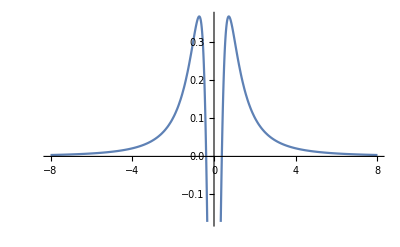

```mathematica
Plot[-(2 Log[2/((1+4 t^2)^(3/2))])/((1+4 t^2)^(3/2)),{t,-8,8}]
```

```mathematica
With[{x=Identity,y=Function[x,Exp[x]]},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

ⅇ^t/((1+ⅇ^(2 t))^(3/2))

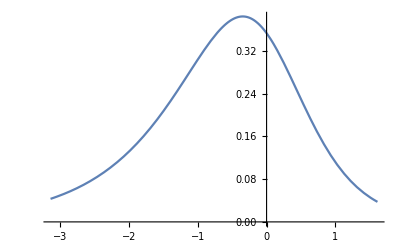

```mathematica
Plot[ⅇ^t/((1+ⅇ^(2 t))^(3/2)),{t,-3.13959465092712,1.6114359150967734}]
```

```mathematica
With[{x=Identity,y=Function[x,x^3]},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

(6 t)/((1+9 t^4)^(3/2))

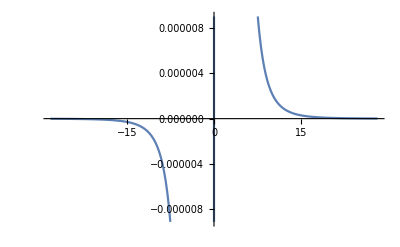

```mathematica
Plot[(6 t)/((1+9 t^4)^(3/2)),{t,-28.21,28.21}]
```

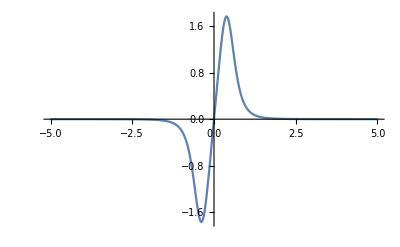

```mathematica
Plot[(6 t)/((1+9 t^4)^(3/2)),{t,-5,5},PlotRange->Full]
```

```mathematica
With[{x=Identity},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

y''[t]/((1+y'[t]^2)^(3/2))

```mathematica
With[{y=Function[t,t^3]},
FullSimplify[y''[t]/((1+y'[t]^2)^(3/2)),t∈Reals]]
```

(6 t)/((1+9 t^4)^(3/2))

```mathematica
Plot[(6 t)/((1+9 t^4)^(3/2)),{t,-28.21,28.21}]
```

-Graphics-

```mathematica
With[{y=Function[t,PDF[NormalDistribution[],t]]},
FullSimplify[y''[t]/((1+y'[t]^2)^(3/2)),t∈Reals]]
```

(PDF^(0,2)[NormalDistribution[0,1],t])/((1+(PDF^(0,1)[NormalDistribution[0,1],t])^2)^(3/2))

```mathematica
PDF[NormalDistribution[],t]
```

(ⅇ^(-t^2/2))/(√(2 π))

```mathematica
With[{y=Function[t,(ⅇ^(-t^2/2))/(√(2 π))]},
FullSimplify[y''[t]/((1+y'[t]^2)^(3/2)),t∈Reals]]
```

(2 ⅇ^(t^2) π (-1+t^2))/((2 ⅇ^(t^2) π+t^2)^(3/2))

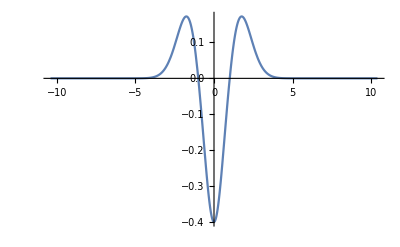

```mathematica
Plot[(2 ⅇ^(t^2) π (-1+t^2))/((2 ⅇ^(t^2) π+t^2)^(3/2)),{t,-10.392304845413262,10.392304845413262},PlotRange->Full]
```

```mathematica
Zeta[3]
```

Zeta[3]

```mathematica
N[Zeta[3]]
```

1.20206

```mathematica
(2 ⅇ^(t^2) π (-1+t^2))/((2 ⅇ^(t^2) π+t^2)^(3/2))
```

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
Manipulate[
Plot[{
x^3,
3 x^2,
(1-a)x^3+a 3 x^2
},{x-2,2}],
{a,0,1}]
```

Plot::pllim: Range specification {-2+x,2} is not of the form {x, xmin, xmax}.

```mathematica
Manipulate[
Plot[{
x^3,
3 x^2,
(1-a)x^3+a 3 x^2
},{x,-2,2}],
{a,0,1}]
```

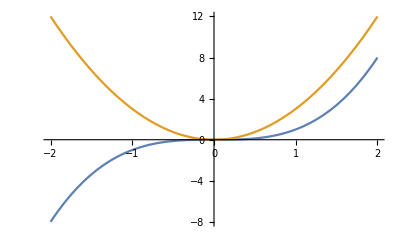

```mathematica
Plot[{x^3,3 x^2},{x,-2,2}]
```

```mathematica
x^3-x
```

-x+x^3

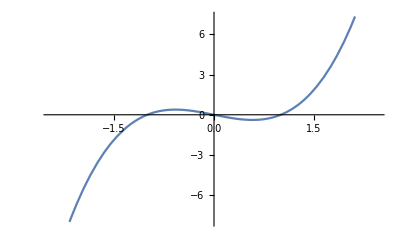

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
x^3-x
```

```mathematica
With[{x=Identity,y=Function[t,t^3-t]},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

(6 t)/((1+(1-3 t^2)^2)^(3/2))

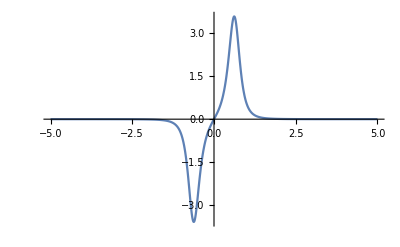

```mathematica
Plot[(6 t)/((1+(1-3 t^2)^2)^(3/2)),{t,-5,5},PlotRange->Full]
```

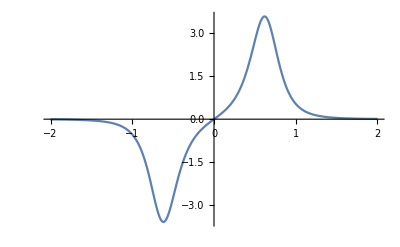

```mathematica
Plot[(6 t)/((1+(1-3 t^2)^2)^(3/2)),{t,-2,2},PlotRange->Full]
```

```mathematica
With[{x=Identity,y=Function[t,t^3-t]},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

```mathematica
Power[(6 t)/((1+(1-3 t^2)^2)^(3/2)),-1]
```

((1+(1-3 t^2)^2)^(3/2))/(6 t)

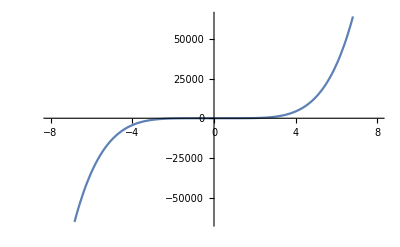

```mathematica
Plot[((1+(1-3 t^2)^2)^(3/2))/(6 t),{t,-8,8}]
```

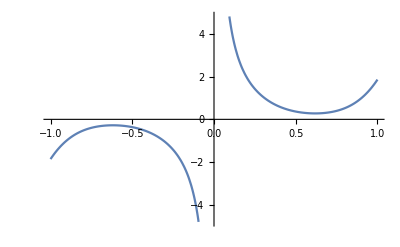

```mathematica
Plot[((1+(1-3 t^2)^2)^(3/2))/(6 t),{t,-1,1}]
```

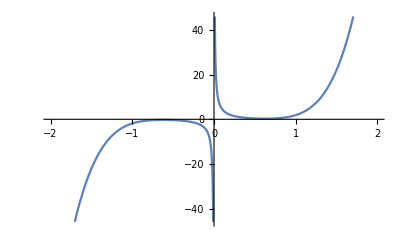

```mathematica
Plot[((1+(1-3 t^2)^2)^(3/2))/(6 t),{t,-2,2}]
```

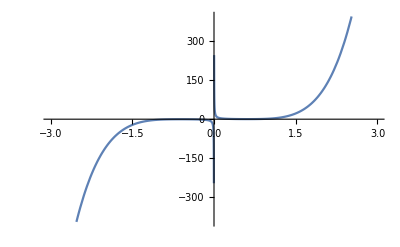

```mathematica
Plot[((1+(1-3 t^2)^2)^(3/2))/(6 t),{t,-3,3}]
```

```mathematica
{t,t^3}+((1+(1-3 t^2)^2)^(3/2))/(6 t)J[D[{t,t^3},t]]/Norm[D[{t,t^3},t]]
```

{t-(t (1+(1-3 t^2)^2)^(3/2))/(2 √(1+9 Abs[t]^4)),t^3+((1+(1-3 t^2)^2)^(3/2))/(6 t √(1+9 Abs[t]^4))}

```mathematica
FullSimplify[
{t-(t (1+(1-3 t^2)^2)^(3/2))/(2 √(1+9 Abs[t]^4)),t^3+((1+(1-3 t^2)^2)^(3/2))/(6 t √(1+9 Abs[t]^4))},t∈Reals]
```

{t-(t (1+(1-3 t^2)^2)^(3/2))/(2 √(1+9 t^4)),t^3+((1+(1-3 t^2)^2)^(3/2))/(6 t √(1+9 t^4))}

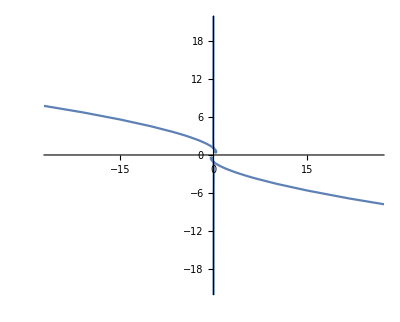

```mathematica
ParametricPlot[{t-(t (1+(1-3 t^2)^2)^(3/2))/(2 √(1+9 t^4)),t^3+((1+(1-3 t^2)^2)^(3/2))/(6 t √(1+9 t^4))},{t,-2,2}]
```

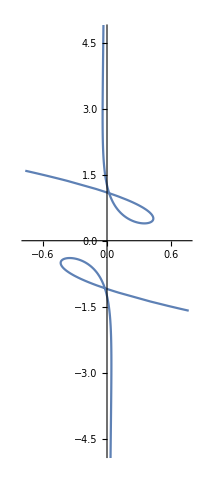

```mathematica
ParametricPlot[{t-(t (1+(1-3 t^2)^2)^(3/2))/(2 √(1+9 t^4)),t^3+((1+(1-3 t^2)^2)^(3/2))/(6 t √(1+9 t^4))},{t,-1,1}]
```

```mathematica
{Cos[t],Sin[t]}+
```

```mathematica
With[{x=Cos,y=Sin},
FullSimplify[(x'[t]y''[t]-x''[t]y'[t])/((√(x'[t]^2+y'[t]^2))^3),t∈Reals]
]
```

1

```mathematica
{Cos[t],Sin[t]}+J[D[{Cos[t],Sin[t]},t]]/Norm[D[{Cos[t],Sin[t]},t]]
```

{Cos[t]-Cos[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2)),Sin[t]-Sin[t]/(√(Abs[Cos[t]]^2+Abs[Sin[t]]^2))}

```mathematica
{Cos[t],Sin[t]}+J[D[{Cos[t],Sin[t]},t]]/Norm[D[{Cos[t],Sin[t]},t]]
```

```mathematica
FullSimplify[{Cos[t],Sin[t]}+J[D[{Cos[t],Sin[t]},t]]/Norm[D[{Cos[t],Sin[t]},t]],t∈Reals]
```

{0,0}

```mathematica
FullSimplify[((√(x'[t]^2+y'[t]^2))^3)/(x'[t]y''[t]-x''[t]y'[t])==1,t∈Reals]
```

((x'[t]^2+y'[t]^2)^(3/2))/(-y'[t] x''[t]+x'[t] y''[t])==1

```mathematica
DSolve[((x'[t]^2+y'[t]^2)^(3/2))/(-y'[t] x''[t]+x'[t] y''[t])==1,{x[t],y[t],x[t],y[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[((x'[t]^2+y'[t]^2)^(3/2))/(-y'[t] x''[t]+x'[t] y''[t])==1,{x[t],y[t],x[t],y[t]},{t}]

```mathematica
With[{x=Cos,y=Sin},
FullSimplify[{x[t],y[t]}+J[D[{x[t],y[t]},t]]/Norm[D[{x[t],y[t]},t]],t∈Reals]
]
```

{0,0}

```mathematica
With[{x=Function[t,t^2],y=Function[t,t^3-t]},
FullSimplify[{x[t],y[t]}+J[D[{x[t],y[t]},t]]/Norm[D[{x[t],y[t]},t]],t∈Reals]
]
```

{t^2+(1-3 t^2)/(√(1-2 t^2+9 t^4)),t (-1+t^2+2/(√(1-2 t^2+9 t^4)))}

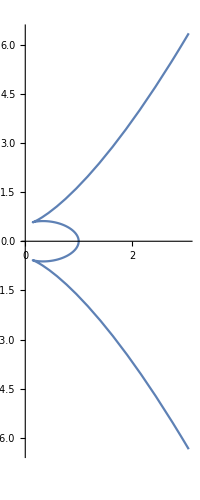

```mathematica
ParametricPlot[{t^2+(1-3 t^2)/(√(1-2 t^2+9 t^4)),t (-1+t^2+2/(√(1-2 t^2+9 t^4)))},{t,-2,2}]
```

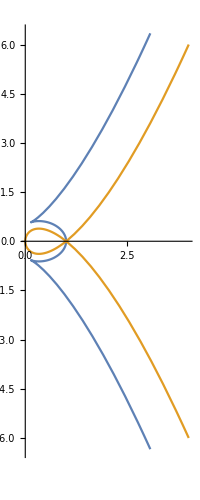

```mathematica
ParametricPlot[{
{t^2+(1-3 t^2)/(√(1-2 t^2+9 t^4)),t (-1+t^2+2/(√(1-2 t^2+9 t^4)))},
{t^2,t(t^2-1)}
},{t,-2,2}]
```

```mathematica
FullSimplify[Normalize@{t,t^3},t∈Reals]
```

{t/(√(t^2+t^6)),(t Abs[t])/(√(1+t^4))}

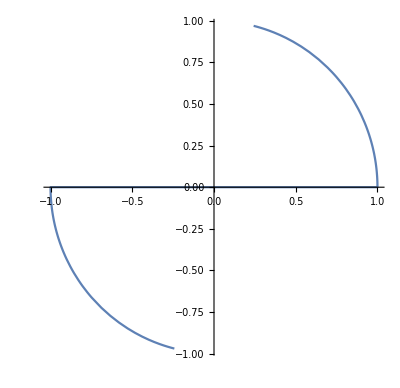

```mathematica
ParametricPlot[{t/(√(t^2+t^6)),(t Abs[t])/(√(1+t^4))},{t,-2,2}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t/(√(t^2+t^6)),(t Abs[t])/(√(1+t^4))},
{t,t^3}
},{t,0,a}],
{a,1,10}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
Manipulate[
ParametricPlot[{
{t/(√(t^2+t^6)),(t Abs[t])/(√(1+t^4))},
{t,t^3}
},{t,0.01,a}],
{a,.1,10}]
```

```mathematica
{t,a^3}
```

```mathematica
Manipulate[
ParametricPlot[{
{t/(√(t^2+t^6)),(t Abs[t])/(√(1+t^4))},
{t,t^3},
{t,a^3 t}
},{t,0.01,a}],
{a,.1,10}]
```

```mathematica
Limit[(f[x+α]-f[x])/α,α->0]
```

lim_(α→0) (-f[x]+f[x+α])/α

```mathematica
FullSimplify[lim_(α->0) (-f[x]+f[x+α])/α]
```

lim_(α→0) (-f[x]+f[x+α])/α

```mathematica
Limit[(Exp[x+α]-Exp[x])/α,α->0]
```

ⅇ^x

```mathematica
Laplacian[f[x,y],{x,y}]==λ f[x,y]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]

```mathematica
Laplacian[f[x],{x}]==λ f[x]
```

f''[x]==λ f[x]

```mathematica
DSolve[f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]}}

```mathematica
ⅇ^(x √λ)+ⅇ^(-x √λ)
```

ⅇ^(-x √λ)+ⅇ^(x √λ)

```mathematica
Manipulate[Plot[ⅇ^(-x √λ)+ⅇ^(x √λ),{x,-3.1597995576900453,3.1597995576900453}],{λ,-1.9498018169219657,1.9498018169219657}]
```

```mathematica
ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]
```

ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]

```mathematica
ReflectionMatrix[a]
```

ReflectionMatrix[a]

```mathematica
ReflectionTransform[v,p]
```

ReflectionTransform[v,p]

```mathematica
ReflectionMatrix[p].{a,b}
```

ReflectionMatrix[p].{a,b}

```mathematica
ReflectionMatrix[π/2].{a,b}
```

ReflectionMatrix::inpv: π/2 is not a vector.

ReflectionMatrix[π/2].{a,b}

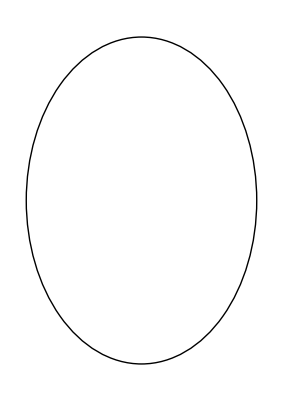

```mathematica
Graphics[GeometricTransformation[Circle[],ShearingTransform[Pi/4,{1,0},{0,1}]]]
```



```mathematica
Graphics[Circle[]]
```

```mathematica
GeometricTransformation[{a,b},ShearingTransform[Pi/4,{1,0},{0,1}]]
```

GeometricTransformation[{a,b},{{{1,1},{0,1}},{0,0}}]

```mathematica
RotationTransform[θ][{a,b}]
```

{a Cos[θ]-b Sin[θ],b Cos[θ]+a Sin[θ]}

```mathematica
ShearingTransform[Pi/4,{1,0},{0,1}][{Cos[t],Sin[t]}]
```

{Cos[t]+Sin[t],Sin[t]}

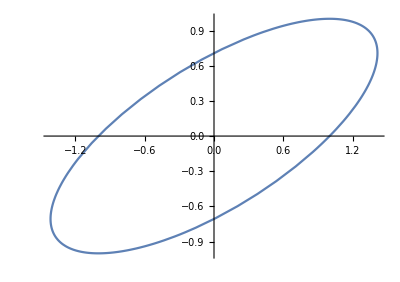

```mathematica
ParametricPlot[{Cos[t]+Sin[t],Sin[t]},{t,0,2π}]
```

```mathematica
With[{gr={Cuboid[],AbsolutePointSize[10],Opacity[1],{Magenta,Point[{0,0,0}]},{Green,Point[{1,1,1}]}}},
Graphics3D[
{{Opacity[.35],Blue,gr},
GeometricTransformation[{Opacity[.85],Red,gr},AffineTransform[{{.8,.5,.5},{0,.8,.5},{0,0,.8}}]]},Boxed->False]
]
```

-Graphics3D-

```mathematica
({x''[t],y''[t]}.J@{x'[t],y'[t]})/(Norm@({x'[t],y'[t]}^3))
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(Abs[x'[t]]^6+Abs[y'[t]]^6))

```mathematica
FullSimplify[({x''[t],y''[t]}.J@{x'[t],y'[t]})/(Norm@({x'[t],y'[t]}^3)),{t,x[t],y[t],x'[t],y'[t],x''[t],y''[t]}∈Reals]
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))

```mathematica
Reals
```

ℝ

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))

```mathematica
(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))==t
```

(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))==t

```mathematica
DSolve[(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))==t,{x[t],y[t],x[t],y[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))==t,{x[t],y[t],x[t],y[t]},{t}]

```mathematica
With[{x=Identity},(-y'[t] x''[t]+x'[t] y''[t])/(√(x'[t]^6+y'[t]^6))==t]
```

y''[t]/(√(1+y'[t]^6))==t

```mathematica
DSolve[y''[t]/(√(1+y'[t]^6))==t,{y[t],y[t]},{t}]
```

{{y[t]→C[2]+InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]K[1]1t}}

```mathematica
{{y[t]->C[2]+InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]K[1]1t}}⟦1,1,2⟧
```

C[2]+InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]K[1]1t

```mathematica
Activate[%%]
```

{{y[t]→C[2]+∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]ⅆK[1]}}

```mathematica
y[t]/.{{y[t]->C[2]+∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]ⅆK[1]}}
```

{C[2]+∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]ⅆK[1]}

```mathematica
First[{C[2]+∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]ⅆK[1]}]
```

C[2]+∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][C[1]+K[1]^2/2]ⅆK[1]

```mathematica
∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][K[1]^2/2]ⅆK[1]
```

∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][K[1]^2/2]ⅆK[1]

```mathematica
∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][K[1]^2/2]ⅆK[1]/.K[1]->x
```

∫_1^t InverseFunction[Hypergeometric2F1[1/6,1/2,7/6,-#1^6] #1&][x^2/2]ⅆx

```mathematica
RotationTransform[π/2][{x,y}]
```

{-y,x}

```mathematica
RotationTransform[π/2][{x,y}]==λ{x,y}
```

{-y,x}=={x λ,y λ}

```mathematica
SolveAlways[{-y,x}=={x λ,y λ},{x,y}]
```

{}

```mathematica
RotationTransform[θ][{x,y}]==λ{x,y}
```

{x Cos[θ]-y Sin[θ],y Cos[θ]+x Sin[θ]}=={x λ,y λ}

```mathematica
(RotationTransform[θ][{x,y}])/{x,y}==λ
```

{(x Cos[θ]-y Sin[θ])/x,(y Cos[θ]+x Sin[θ])/y}==λ

```mathematica
{(x Cos[θ]-y Sin[θ])/x,(y Cos[θ]+x Sin[θ])/y}==λ/.θ->π/2
```

{-y/x,x/y}==λ

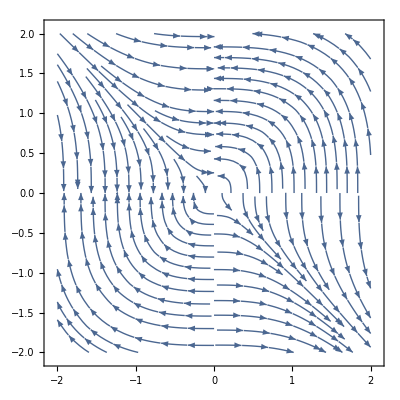

```mathematica
StreamPlot[{-y/x,x/y},{x,-2,2},{y,-2,2}]
```

```mathematica
StreamPlot[{-y/x,x/y},{x,-2,2},{y,-2,2},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
RotationTransform[θ][{t,f[t]}]==λ{t,f[t]}
```

{t Cos[θ]-f[t] Sin[θ],Cos[θ] f[t]+t Sin[θ]}=={t λ,λ f[t]}

```mathematica
{t Cos[θ]-f[t] Sin[θ],Cos[θ] f[t]+t Sin[θ]}/{t,f[t]}==λ
```

{(t Cos[θ]-f[t] Sin[θ])/t,(Cos[θ] f[t]+t Sin[θ])/f[t]}==λ

```mathematica
{(t Cos[θ]-f[t] Sin[θ])/t,(Cos[θ] f[t]+t Sin[θ])/f[t]}==λ/.θ->π/2
```

{-f[t]/t,t/f[t]}==λ

```mathematica
With[{f=Sin},{-f[t]/t,t/f[t]}==λ]
```

{-Sin[t]/t,t Csc[t]}==λ

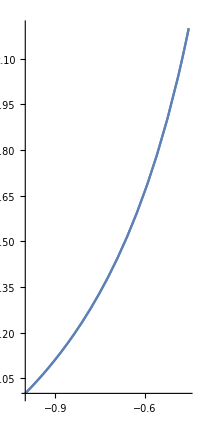

```mathematica
ParametricPlot[{-Sin[t]/t,t Csc[t]},{t,-2,2}]
```

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
f'[x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
ⅇ^(x λ) C[1]
```

ⅇ^(x λ) C[1]

```mathematica
Integrate[f'[x],x]==λ f'[x]
```

f[x]==λ f'[x]

```mathematica
DSolve[f[x]==λ f'[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x/λ) C[1]}}

```mathematica
Exp[f'[x]/f[x]]==λ f[x]
```

ⅇ^(f'[x]/f[x])==λ f[x]

```mathematica
DSolve[ⅇ^(f'[x]/f[x])==λ f[x],{f[x]},{x}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{f[x]→(ⅇ^(ⅇ^(x+C[1])))/λ}}

```mathematica
Solve[ⅇ^(f'[x]/f[x])==λ f[x],λ]
```

{{λ→ⅇ^(f'[x]/f[x])/f[x]}}

```mathematica
Laplacian[f[x],{x}]==λ f[x]
```

f''[x]==λ f[x]

```mathematica
DSolve[f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]}}

```mathematica
DSolve[f''[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x √λ) C[1]+ⅇ^(-x √λ) C[2]}}

```mathematica
1/2==∫_0^a x^2 ⅆx
```

1/2==a^3/3

```mathematica
Solve[1/2==a^3/3,{a}]
```

{{a→-(-3/2)^(1/3)},{a→(3/2)^(1/3)},{a→(-1)^(2/3) (3/2)^(1/3)}}

```mathematica
Reduce[1/2==a^3/3]
```

a==-(-3/2)^(1/3)||a==(3/2)^(1/3)||a==(-1)^(2/3) (3/2)^(1/3)

```mathematica
1/2==a^3/3
```

```mathematica
(3/2)^(1/3)
```

```mathematica
1==∫_-a^a x^2 ⅆx
```

1==(2 a^3)/3

```mathematica
Solve[1==(2 a^3)/3,{a}]
```

{{a→-(-3/2)^(1/3)},{a→(3/2)^(1/3)},{a→(-1)^(2/3) (3/2)^(1/3)}}

```mathematica
∫_(-(3/2)^(1/3))^((3/2)^(1/3)) x^2 ⅆx
```

1

```mathematica
∫_(-(3/2)^(1/3))^((3/2)^(1/3)) x^2 Log[x^2]ⅆx
```

2/3 (-1+Log[3/2])

```mathematica
∫(x^2 Log[x^2])ⅆx
```

-(2 x^3)/9+1/3 x^3 Log[x^2]

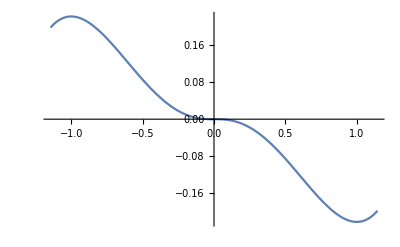

```mathematica
Plot[-(2 x^3)/9+1/3 x^3 Log[x^2],{x,-(3/2)^(1/3),(3/2)^(1/3)}]
```

```mathematica
∫(-x^2 Log[x^2])ⅆx
```

(2 x^3)/9-1/3 x^3 Log[x^2]

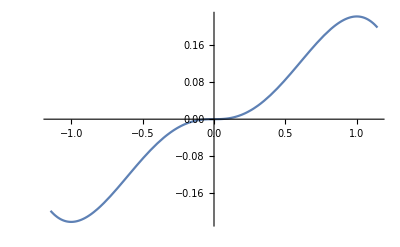

```mathematica
Plot[(2 x^3)/9-1/3 x^3 Log[x^2],{x,-(3/2)^(1/3),(3/2)^(1/3)}]
```

```mathematica
{(2a Exp[b t]Cos[t])/(1+a^2 Exp[2b t]),(2a Exp[b t]Sin[t])/(1+a^2 Exp[2b t]),(a^2 Exp[2 b t]-1)/(1+a^2 Exp[2b t])}
```

{(2 a ⅇ^(b t) Cos[t])/(1+a^2 ⅇ^(2 b t)),(2 a ⅇ^(b t) Sin[t])/(1+a^2 ⅇ^(2 b t)),(-1+a^2 ⅇ^(2 b t))/(1+a^2 ⅇ^(2 b t))}

```mathematica
{(2 a ⅇ^(b t) Cos[t])/(1+a^2 ⅇ^(2 b t)),(2 a ⅇ^(b t) Sin[t])/(1+a^2 ⅇ^(2 b t)),(-1+a^2 ⅇ^(2 b t))/(1+a^2 ⅇ^(2 b t))}/.{a->1,b->1}
```

{(2 ⅇ^t Cos[t])/(1+ⅇ^(2 t)),(2 ⅇ^t Sin[t])/(1+ⅇ^(2 t)),(-1+ⅇ^(2 t))/(1+ⅇ^(2 t))}

```mathematica
ParametricPlot3D[{(2 ⅇ^t Cos[t])/(1+ⅇ^(2 t)),(2 ⅇ^t Sin[t])/(1+ⅇ^(2 t)),(-1+ⅇ^(2 t))/(1+ⅇ^(2 t))},{t,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(2 ⅇ^t Cos[t])/(1+ⅇ^(2 t)),(2 ⅇ^t Sin[t])/(1+ⅇ^(2 t)),(-1+ⅇ^(2 t))/(1+ⅇ^(2 t))},{t,0,8π}]
```

-Graphics3D-

```mathematica
{(2 a ⅇ^(b t) Cos[t])/(1+a^2 ⅇ^(2 b t)),(2 a ⅇ^(b t) Sin[t])/(1+a^2 ⅇ^(2 b t)),(-1+a^2 ⅇ^(2 b t))/(1+a^2 ⅇ^(2 b t))}/.{a->1,b->.15}
```

{(2 ⅇ^(0.15 t) Cos[t])/(1+ⅇ^(0.3 t)),(2 ⅇ^(0.15 t) Sin[t])/(1+ⅇ^(0.3 t)),(-1+ⅇ^(0.3 t))/(1+ⅇ^(0.3 t))}

```mathematica
ParametricPlot3D[{(2 ⅇ^(0.15 t) Cos[t])/(1+ⅇ^(0.3 t)),(2 ⅇ^(0.15 t) Sin[t])/(1+ⅇ^(0.3 t)),(-1+ⅇ^(0.3 t))/(1+ⅇ^(0.3 t))},{t,0,2π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{u^3,v^3,u v}, {u,v}∈Disk[]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{u^3,v^3,u v}, {u,v}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{u^3,v^3,u v}, {u,v}∈Disk[{0,0},5]]
```

-Graphics3D-

```mathematica
Grad@{u^3,v^3,u v}
```

Grad::argtu: Grad called with 1 argument; 2 or 3 arguments are expected.

Grad[{u^3,v^3,u v}]

```mathematica
Grad[{u^3,v^3,u v},{u,v}]
```

{{3 u^2,0},{0,3 v^2},{v,u}}

```mathematica
Div[{u^3,v^3,u v},{u,v}]
```

Div::ndimv: There is no 2-dimensional divergence for the 3-dimensional vector {u^3,v^3,u v}.

{u^3,v^3,u v}{u,v}